# In silico analysis of corticosteroid-boosted antibiotics treatment for septic arthritis in a hybrid mathematical model

```mathematica
T=5150
```

5150

## Antibiotic treatment without corticosteroids

```mathematica
dataABOnly = Import["C:\\Users\\Juhász Nóra\\Documents\\HAL-master\\CorticosteroidsAntibiotics\\output\\StaphyloExperiments\\AntibioticsOnly\\Out.csv","Data"];
```

Data: tick, healthy, infected, dead, bacteria, immune,  AB, CS

```mathematica
dataABOnly[[2]]
```

{0,10000.,0.,0.,27.27,10.,0.,0.}

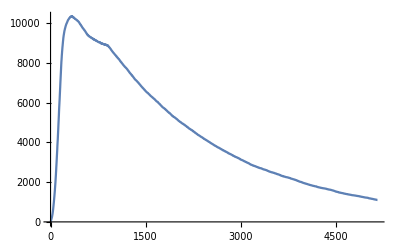

```mathematica
bactDataABOnly=Table[dataABOnly[[i]][[5]],{i,1,T}];
immuneDataABOnly=Table[dataABOnly[[i]][[6]],{i,1,T}];
ABDataABOnly=Table[dataABOnly[[i]][[7]],{i,1,T}];
CSDataABOnly=Table[dataABOnly[[i]][[8]],{i,1,T}];
ListLinePlot[{immuneDataABOnly},PlotRange->All]
```

Nem annyira sima, mint amilyennek látszik, illetve a fent látszódó “töréspont” sem annyira egyedi, mint látszik:

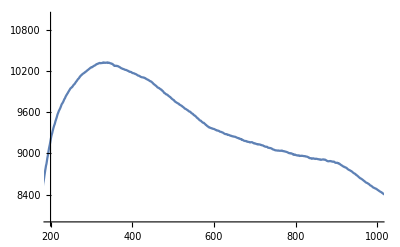

```mathematica
ListLinePlot[{immuneDataABOnly},PlotRange->{{200,1000},{8000,11000}}]
```

A kódban több fix threshold is van, ami okozhat ilyeneket. Pl.: egy neutrofil csak akkor tud továbbiakat hívni, ha a saját location-jén nincs több, mint 4 neutrofil. Ez pl. azt jelenti, hogy ha kialakult egy nagyon “telített” helyzet, mint fent, akkor egy ideig nagyrészt csak csökkenni fog a számuk, újakat hívni a legtöbbjük nem fog tudni (ez a mozgásuk miatt persze egyedenként változhat). Mikor a sűrűségük lecsökken annyira, hogy egy adott helyen már nincs telítődve az immunrendszer, akkor ezek a neutrofilok képesek újakat hívni. A fenti képen a baktériumok koncentrációja továbbra is alacsony, így továbbra is csökken a neutrofilok száma, de ennek a csökkenésnek a mértéke enyhén lassul 600 körül, amit magyarázhat a rendszernez ez telítődés jellegű feature-e.

Threshold-ok a kódban, amik miatt a megjelenő görbéktől tökéletes simaságot nem várhatunk:
- pop < 5 feltétel
- arrivalFactor > 1 feltétel
- extinction feltétel

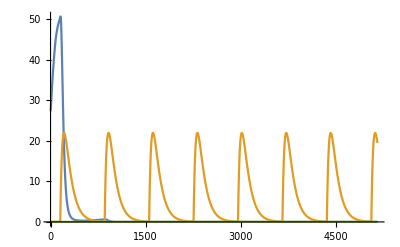

```mathematica
ListLinePlot[{bactDataABOnly,ABDataABOnly,CSDataABOnly},PlotRange->All]
```

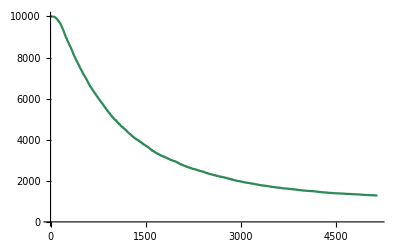

```mathematica
healthyCellDataABOnly =Table[dataABOnly[[i]][[2]],{i,1,T}];
ListLinePlot[{healthyCellDataABOnly},PlotRange->{0,10000},PlotStyle->Directive[ColorData["Legacy","SeaGreen"]]]
```

Észrevételek:
- a kortikoszteroid nélküli AB kezelés a baktériumok nagyon gyors eliminációját adja. Gyakorlatilag 2 adag (de nem egy!) után lenullázódik a fertőzés. Itt nincs szteroid -> AB + erős immunreakció --> gyors baktérium-eltörlés, de
- nagyon jelentős porckárosodás

## Antibiotic treatment with corticosteroids

```mathematica
T=5150
```

5150

```mathematica
dataCSboostedAB = Import["C:\\Users\\Juhász Nóra\\Documents\\HAL-master\\CorticosteroidsAntibiotics\\output\\StaphyloExperiments\\steroidBoostedAB\\Out.csv","Data"];
```

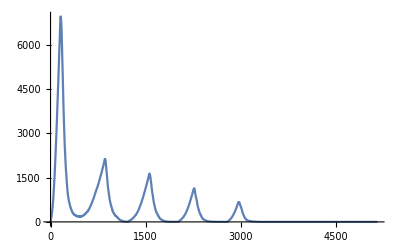

```mathematica
bactDataCSboostedAB=Table[dataCSboostedAB[[i]][[5]],{i,1,T}];
immuneDataCSboostedAB=Table[dataCSboostedAB[[i]][[6]],{i,1,T}];
ABDataCSboostedAB=Table[dataCSboostedAB[[i]][[7]],{i,1,T}];
CSDataCSboostedAB=Table[dataCSboostedAB[[i]][[8]],{i,1,T}];
ListLinePlot[{immuneDataCSboostedAB},PlotRange->All]
```

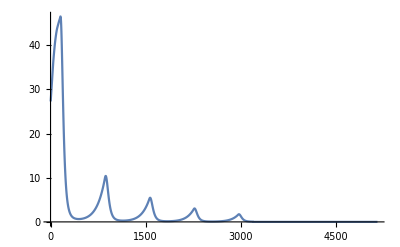

```mathematica
ListLinePlot[bactDataCSboostedAB, PlotRange->All]
```

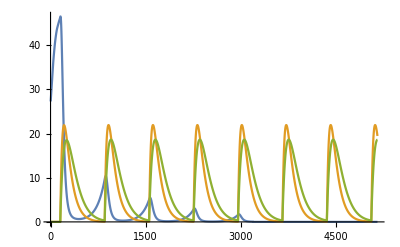

```mathematica
ListLinePlot[{bactDataCSboostedAB,ABDataCSboostedAB,CSDataCSboostedAB}, PlotRange->All]
```

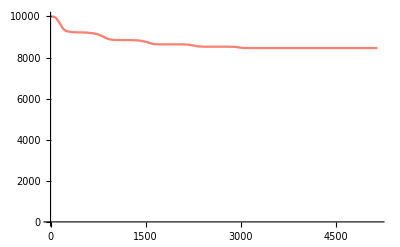

```mathematica
healthyCellDataCSboostedAB =Table[dataCSboostedAB[[i]][[2]],{i,1,T}];
ListLinePlot[{healthyCellDataCSboostedAB},PlotRange->{0,10000},PlotStyle->Directive[ColorData["Legacy","Salmon"]]]
```

Észrevételek:
- itt az AB “egyedül” küzd a fertőzés ellen a kezelés megkezdése után, különösen azokban az időablakokban, ahol magas a CS szint.
- hullámok alakulnak ki:
	a) a baktériumok számában hullámok látszanak, a növekedő szakaszok akkor jelennek meg, mikor alacsony az AB szint
	b) az immunsejtek számában a baktrérium-hullámokat követő hullámok alakulnak ki
- a kezelés uralni tudja a fertőzést, de lassabban húzza le azt, mint ha csak AB-t kapna a beteg
- cserébe a porc sokkal kevésbé károsodik

```mathematica
Rasterize[ListLinePlot[
{healthyCellDataABOnly,healthyCellDataCSboostedAB},
PlotRange->{0,10000},
PlotStyle->{Directive[ColorData["Legacy","SeaGreen"]],Directive[ColorData["Legacy","Salmon"]]},Background->Lighter[Gray, 0.9],
Frame->True,
PlotLabel->Style["Az egészséges sejtek számának alakulása",FontSize->14],
FrameLabel->{{"egészséges sejtek száma",""},{"idő (mért. egys. nélküli időegység)",""}},
PlotLegends->{"csak antibiotikum","kortikoszteroid és antibiotikum"}]]
```

-Graphics-

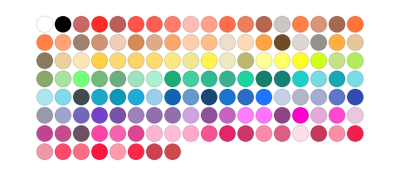

```mathematica
ColorData["Crayola","Panel"]
```